```mathematica
ClearAll["Global`*"]
```

q0 Is the initial mortality rate for an organism of mass M
If M is grams, a0 = 0.594 (1.88*10^-8 sec) and b0 = -0.56

```mathematica
q0 = a0*M^b0;
```

α is the Gompertz constant for actuarial aging rate... it is the annual rate of increase in mortality; if M is grams, a1 = 4.45 (1.45*10^-7 sec); b1 = -0.27

```mathematica
α = a1*M^b1;
```

Life expectancy
a2 = 4.04*10^6 seconds gram^-b2; b2 = 0.30

```mathematica
texp = a2*M^b2;
```

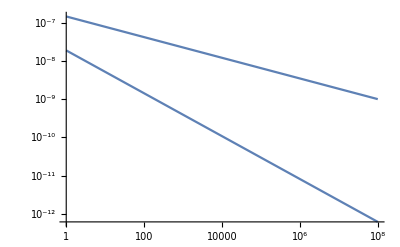

```mathematica
LogLogPlot[{q0,α}/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27},{M,1,10^8}]
```

The Gompertz Equation: number of surviving from previous year... so t is in a population’s lifetime, and n(t) is the number of individuals surviving from year to year.

```mathematica
n = n0*Exp[q0/α*(1-Exp[α*t])];
```

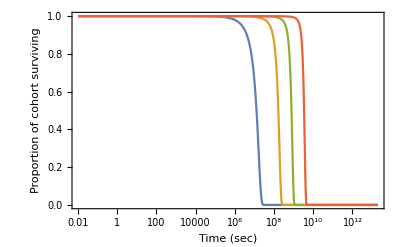

```mathematica
masses={1,10^3,10^5,10^7};
Show[
Table[LogLinearPlot[n/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,n0->1,M->masses[[i]]},{t,0.01,20000000000000},PlotRange->All,PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Time (sec)","Proportion of cohort surviving"},LabelStyle->Directive[FontSize->16]],{i,1,4}]
]
```

```mathematica
mortratetime = FullSimplify[-D[n,t]*(1/n)]
```

a0 ⅇ^(a1 M^b1 t) M^b0

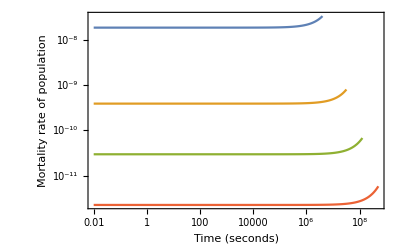

```mathematica
With[{a0=1.88*10^-8,b0=-0.56,a1=1.45*10^-7,b1=-0.27,a2=4.04*10^6,b2=0.30},
masses={1,10^3,10^5,10^7};
tend = a2*masses^b2;
Show[
Table[LogLogPlot[a0 ⅇ^(a1 M^b1 t) M^b0/.M->masses[[i]],{t,0.01, tend[[i]]},PlotRange->All,PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Time (seconds)","Mortality rate of population"},LabelStyle->Directive[FontSize->16]],{i,1,4}]
]
]
```

```mathematica
(*avgmortrate = (1/texp)*Integrate[mortratetime,{t,0,texp}]*)
```

```mathematica
(*LogLogPlot[avgmortrate/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},{M,1,10^7}]*)
```

Altering expected mortality patterns via external predation/hunting

IMPORTANT... if we expect hunting to impact the aging rate, it should impact α
...if we expect hunting to impact the initial mortality rate, it should impact q0
For now it might just be easier to assume that it impacts q0... if it impacts α, increasing α for a particular Mass means that there are fewer older age classes (predators are extracting the older prey). If q0 is higher, I think this means that there is larger uniform mortality

Here is a very simplistic one... we have the scalings of intial mortality rate q0... and scalings for the annual rate of increase in mortality α with just an added mass independent term.

```mathematica
(*With[{a0=1.88*10^-8,b0=-0.56,a1=1.45*10^-7,b1=-0.27},
q0 = a0*M^b0;
q0adj = a0*M^b0;
(*q0 Is the initial mortality rate for an organism of mass M*)
α=a1*M^b1;
αadj=a1*M^b1 ;
(*α is the Gompertz constant for actuarial aging rate... it is the annual rate of increase in mortality*)
Manipulate[
LogLogPlot[{q0,α,a0*M^b0+ξ},{M,1,10^8},Frame->True,FrameLabel->{"Mass (g)","Life history mortality rates (1/s)"}],{ξ,0,0.000001}]
]*)
```

If we want an additional mass-dependent mortality... we could use the predation window defined by Rohr to capture the additional mortality within a particular link-probability window... so that gives us pr(link) = f(M)... then predationmortality = ξf(M) for a particular predator size M_p

```mathematica
nsurvivors = n0*Exp[q0/α*(1-Exp[α*t])]
```

ⅇ^((a0 (1-ⅇ^(a1 M^b1 t)) M^(b0-b1))/a1) n0

```mathematica
nsurv[q0_,α_,n0_] :=ⅇ^(((1-ⅇ^(t α)) q0)/α) n0
```

```mathematica
mortcohort=(-D[nsurvivors,t]*(1/(nsurvivors)))
```

a0 ⅇ^(a1 M^b1 t) M^b0

```mathematica
mortcorhortrate[q0_,α_] :=ⅇ^(t α) q0
```

```mathematica
avgmort=(1/texp)* Integrate[mortcohort,{t,0,texp}]
```

(a0 (-1+ⅇ^(a1 a2 M^(b1+b2))) M^(b0-b1-b2))/(a1 a2)

```mathematica
avgmortrate[q0_,α_,texp_]:=((-1+ⅇ^(texp α)) q0)/(texp α)
```

Here is the average mortality rate as a function of 
[q0: initial mortality rate (1/s); α: actuarial mortality rate (1/s); texp: expected lifespan (s)]

```mathematica
avgmortratescaled[M_]:=avgmortrate[(a0*M^b0)*(1+chiq0),( a1*M^b1)*(1+chia), a2*M^b2]
```

```mathematica
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
m0[M_]:=0.097*M^0.92;
ϵLam = 0.95;
```

```mathematica
MortalityReproductionRatio[M_]:=avgmortratescaled[M]/λ[M]
```

```mathematica
MortalityReproductionRatio[M]
```

-(0.0227521 (1+chiq0) (-1+ⅇ^(0.5858 (1+chia) M^0.03)) Log[0.0127415/(1-0.558075/M^0.02)])/((1+chia) M^0.34)

```mathematica
epilog1=ContourPlot[MortalityReproductionRatio[M]/.M->100,{chiq0,-1,10},{chia,-1,10},Contours->{{1.0,Thick}},ContourShading->None][[1]];
epilog2=ContourPlot[MortalityReproductionRatio[M]/.M->10000000,{chiq0,-1,10},{chia,-1,10},Contours->{{1.0,Thick}},ContourShading->None][[1]];
```

```mathematica
DP1=
Show[{
DensityPlot[MortalityReproductionRatio[M]/.M->100,{chiq0,-1,10},{chia,-1,10},PlotRange->{0,2},ColorFunction->"DarkRainbow",Epilog->epilog1,FrameLabel->{"Prop. change q_0","Prop. change q_a"},ImageSize->400,LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[Automatic,LegendLabel->"μ/λ_C^max",LegendMarkerSize->180]],
Graphics[Text[Style["M_C = 10^2 g",15],{7,9.5}]](*,
ListPlot[{{-0.99,0},{10,0}},PlotStyle->{White,PointSize[Large]}],
ListPlot[{{-0.99,0},{10,0}},PlotStyle->{White,PointSize[Large]},Joined->True],
ListPlot[{{0,-0.99},{0,10}},PlotStyle->{White,PointSize[Large]}],
ListPlot[{{0,-0.99},{0,10}},PlotStyle->{White,PointSize[Large]},Joined->True]*)
},ImageSize->250];
DP2=
Show[{
DensityPlot[MortalityReproductionRatio[M]/.M->1000000,{chiq0,-1,10},{chia,-1,10},PlotRange->{0,2},ColorFunction->"DarkRainbow",Epilog->epilog2,FrameLabel->{"Prop. change q_0","Prop. change q_a"},ImageSize->400,LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[Automatic,LegendLabel->"μ/λ_C^max",LegendMarkerSize->180]],
Graphics[Text[Style["M_C = 10^6 g",15],{7,9.5}]](*,
ListPlot[{{0,-0.99},{0,10}},PlotStyle->{White,PointSize[Large]}],
ListPlot[{{0,-0.99},{0,10}},PlotStyle->{White,PointSize[Large]},Joined->True]*)
},ImageSize->250];
```

```mathematica
DPRow=GraphicsRow[{
DP1,DP2
},ImageSize->650,Spacings->Scaled[0.]]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_naturalmortalityratio.pdf"}],DPRow,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_naturalmortalityratio.pdf

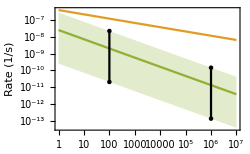

```mathematica
q0Plot = 
Show[{
LogLogPlot[{
avgmortratescaled[M]/.{chiq0->0,chia->0},
λ[M],
avgmortratescaled[M]/.{chiq0->10,chia->0},
avgmortratescaled[M]/.{chiq0->-0.99,chia->0}},{M,1,10^7},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Rate (1/s)"},
PlotStyle->{ColorData[97,3],ColorData[97,2],Transparent,Transparent},Filling->{4->{{3},{Directive[{ColorData[97,3],Opacity[0.25]}]}}},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[
{{10^2,avgmortratescaled[M]/.{M->10^2,chiq0->-0.99,chia->0}},
{10^2,avgmortratescaled[M]/.{M->10^2,chiq0->10,chia->0}},
},Joined->False,PlotStyle->Black],
ListLogLogPlot[
{{10^2,avgmortratescaled[M]/.{M->10^2,chiq0->-0.99,chia->0}},
{10^2,avgmortratescaled[M]/.{M->10^2,chiq0->10,chia->0}},
},Joined->True,PlotStyle->Black],
ListLogLogPlot[
{{10^6,avgmortratescaled[M]/.{M->10^6,chiq0->-0.99,chia->0}},
{10^6,avgmortratescaled[M]/.{M->10^6,chiq0->10,chia->0}}
},Joined->False,PlotStyle->Black],
ListLogLogPlot[
{{10^6,avgmortratescaled[M]/.{M->10^6,chiq0->-0.99,chia->0}},
{10^6,avgmortratescaled[M]/.{M->10^6,chiq0->10,chia->0}}
},Joined->True,PlotStyle->Black]
},ImageSize->250]
```

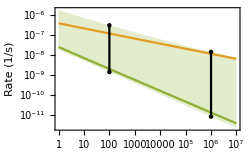

```mathematica
qaPlot = 
Show[{
LogLogPlot[{
avgmortratescaled[M]/.{chiq0->0,chia->0},
λ[M],
avgmortratescaled[M]/.{chiq0->0,chia->10},
avgmortratescaled[M]/.{chiq0->0,chia->-0.99}},{M,1,10^7},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Rate (1/s)"},PlotStyle->{ColorData[97,3],ColorData[97,2],Transparent,Transparent},Filling->{4->{{3},{Directive[{ColorData[97,3],Opacity[0.25]}]}}},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[
{{10^2,avgmortratescaled[M]/.{M->10^2,chia->-0.99,chiq0->0}},
{10^2,avgmortratescaled[M]/.{M->10^2,chia->10,chiq0->0}},
},Joined->False,PlotStyle->Black],
ListLogLogPlot[
{{10^2,avgmortratescaled[M]/.{M->10^2,chia->-0.99,chiq0->0}},
{10^2,avgmortratescaled[M]/.{M->10^2,chia->10,chiq0->0}},
},Joined->True,PlotStyle->Black],
ListLogLogPlot[
{{10^6,avgmortratescaled[M]/.{M->10^6,chia->-0.99,chiq0->0}},
{10^6,avgmortratescaled[M]/.{M->10^6,chia->10,chiq0->0}}
},Joined->False,PlotStyle->Black],
ListLogLogPlot[
{{10^6,avgmortratescaled[M]/.{M->10^6,chia->-0.99,chiq0->0}},
{10^6,avgmortratescaled[M]/.{M->10^6,chia->10,chiq0->0}}
},Joined->True,PlotStyle->Black]
},ImageSize->250]
```

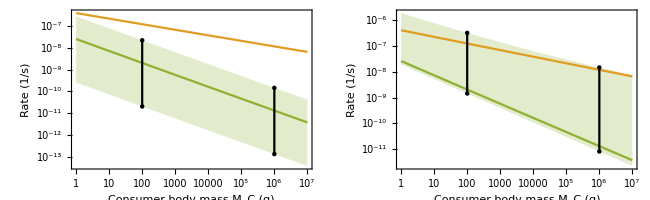

```mathematica
qRow = GraphicsRow[{q0Plot,qaPlot},ImageSize->650,Spacings->Scaled[0]]
```

```mathematica
DPqPlot = GraphicsColumn[{DPRow,qRow},ImageSize->680,Spacings->Scaled[0]]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_naturalmortalityratio_rev.pdf"}],DPqPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_naturalmortalityratio_rev.pdf